## Convolution With Mathematica

Chengjun Wang @ Web mining Lab

```mathematica
f[x_]=Piecewise[{{0.682,-0.326<x<0.652},{0.454,-1.793<x<-1.304}, {0.227, 1.630<x<2.119}}]
```

Piecewise[{{0.682, -0.326<x<0.652}, {0.454, -1.793<x<-1.304}, {0.227, 1.63<x<2.119}, {0, True}}]

```mathematica
(* Define Piecewise Function
```

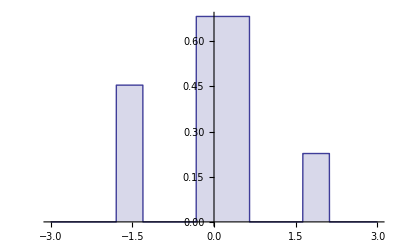

```mathematica
Plot[f[x],{x,-3,3},Filling->Bottom,Exclusions->None]
```

```mathematica
(* Write the function that defines the convolution of f with itself
```

```mathematica
fftx=FourierTransform[f[t],t,w]
```

(ⅇ^(-1.5485 ⅈ w) ((0.908+0.454 ⅇ^(3.423 ⅈ w)) Sin[0.2445 w]+1.364 ⅇ^(1.7115 ⅈ w) Sin[0.489 w]))/(√(2 π) w)

```mathematica
fftxp=PolarPlot[fftx,{w,-5,5}]
```

-Graphics-

```mathematica
ffsx=FourierSinTransform[f[t],t,w]
```

(1.364-1.364 Cos[0.652 w]+0.454 Cos[1.63 w]-0.454 Cos[2.119 w])/(√(2 π) w)

```mathematica
ffcx=FourierCosTransform[f[x],x,w]
```

(1.364 Sin[0.652 w]-0.454 Sin[1.63 w]+0.454 Sin[2.119 w])/(√(2 π) w)

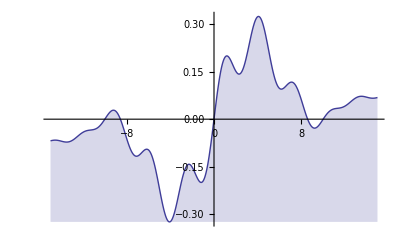

```mathematica
ffsxp=Plot[ffsx,{w,-15,15},Filling->Bottom,Exclusions->None]
```

```mathematica
ffcxp=Plot[ffcx,{w,-15,15},Filling->Bottom,Exclusions->None]
```

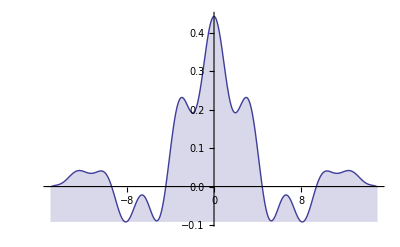

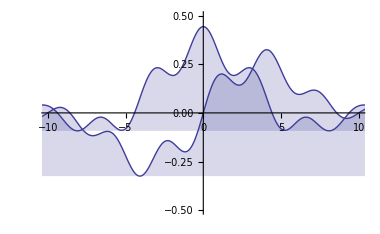

```mathematica
Show[ffsxp,ffcxp, PlotRange->{{-10,10},{-.5,.5}}]
```

```mathematica
g[t_]=Integrate[f[x]*f[t-x],{x,-Infinity,Infinity}]
```

Piecewise[{{0.151408, 1.793<t≤2.282}, {0.302816, -1.63<t≤-1.141}, {4.×10^-9 (1.93627×10^8-1.6781×10^8 t), 0.326<t<0.815}, {0.00103058 (-163.+50. t), 3.26<t≤3.749}, {-0.00372099 (-163.+125. t), 0.815≤t<1.304}, {0.00247702 (-163.+125. t), 1.304<t≤1.793}, {-0.00164893 (326.+125. t), -3.097<t<-2.608}, {-0.00247702 (163.+250. t), -1.141<t<-0.652}, {0.0018605 (163.+250. t), -0.652<t≤-0.163}, {-0.000103058 (-2119.+500. t), 3.749<t<4.238}, {0.000412232 (1793.+500. t), -3.586<t≤-3.097}, {-0.000309628 (-2771.+1000. t), 2.282<t<2.771}, {0.000619256 (2119.+1000. t), -2.119<t≤-1.63}, {4.×10^-9 (8.42144×10^7+1.6781×10^8 t), -0.163<t≤0.326}, {0., True}}]

```mathematica
Convolve[g[t],g[t],t,t1]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

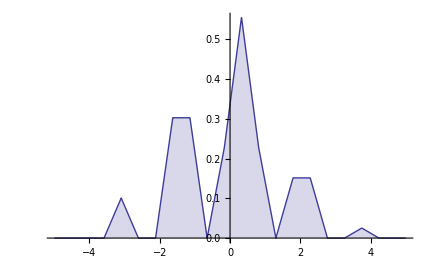

```mathematica
Plot[g[t],{t,-5,5},Filling->Bottom ,Exclusions->None]
```

```mathematica
(* A convolution typically smooths the function
```

```mathematica
ffsxg=FourierSinTransform[g[x],x,w]
```

1/(√(2 π) w^2)(0.673716 w-3.80883×10^-17 w Cos[1.793 w]+3.80883×10^-17 w Cos[2.282 w]+2.68496 Sin[0.326 w]-0.412232 Sin[0.815 w]-1.5495 Sin[1.304 w]+0.619256 Sin[1.793 w]+0.619256 Sin[2.282 w]-0.619256 Sin[2.771 w]-0.103058 Sin[3.26 w]+0.206116 Sin[3.749 w]-0.103058 Sin[4.238 w])

```mathematica
ffcxg=FourierCosTransform[g[x],x,w]
```

1/(√(2 π) w^2)(-1.34248+2.68496 Cos[0.326 w]-0.412232 Cos[0.815 w]-1.5495 Cos[1.304 w]+0.619256 Cos[1.793 w]+0.619256 Cos[2.282 w]-0.619256 Cos[2.771 w]-0.103058 Cos[3.26 w]+0.206116 Cos[3.749 w]-0.103058 Cos[4.238 w]+3.80883×10^-17 w Sin[1.793 w]-3.80883×10^-17 w Sin[2.282 w])

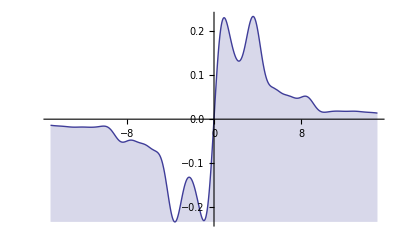

```mathematica
ffsxpg=Plot[ffsxg,{w,-15,15},Filling->Bottom,Exclusions->None]
```

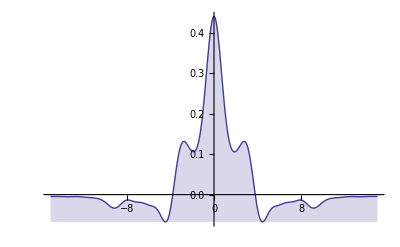

```mathematica
ffcxpg=Plot[ffcxg,{w,-15,15},Filling->Bottom,Exclusions->None]
```

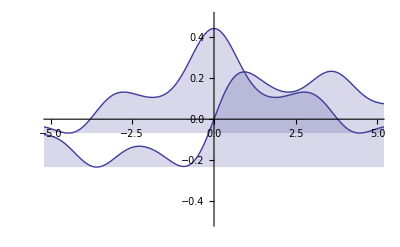

```mathematica
Show[ffsxpg, ffcxpg, PlotRange->{{-5,5},{-.5,.5}}]
```

```mathematica
h[u_]=Integrate[g[t]*g[u-t],{t,-Infinity,Infinity}]
```

∫_(-∞)^∞ g[t] g[-t+u]ⅆt

```mathematica
Plot[h[u], {u,-3,3},Filling->Bottom,Exclusions->None]
```

```mathematica
f0=UnitBox[t0]
```

UnitBox[t0]

```mathematica
f1=Convolve[f0,f0,t0,t1]
```

UnitTriangle[t1]

```mathematica
f2=Convolve[f1,f1,t1,t2]
```

Piecewise[{{1/6 (4-6 t2^2-3 t2^3), -1<t2<0}, {-1/6 t2 (6+6 t2+t2^2), t2==-1}, {-1/6 (-2+t2)^3, 1<t2<2}, {1/3 (2-3 t2+t2^3), t2==0}, {1/6 t2 (6-6 t2+t2^2), t2==1}, {1/6 (2+t2)^3, -2<t2<-1}, {1/6 (4-6 t2^2+3 t2^3), 0<t2<1}, {0, True}}]

```mathematica
{{0.002477024 (-163.+125. t), 1.304<t≤1.793}}
```